```mathematica
(* Set machine precision at start *)
$PreRead=(#/.s_String/;StringMatchQ[s,NumberString]&&Precision@ToExpression@s==MachinePrecision:>s<>"`400."&);
(* Matlab style linspace and logspace *)
linspace[start_,stop_,n_:100]:=start + (stop-start)*Subdivide[n-1];
linspace[start_,stop_,1]:=stop;
logspace[start_,stop_,n_:100]:=10.0^linspace[start,stop,n];
```

## Limit on summations for given M·p or M·(1-p) in double precision

#### Summation terms for small values of M·p

Define the vector containing the number of trials M and the relation between p and M, i.e. p = α/M where α is an element of pfactor vector

```mathematica
numM = 40;
M = N[Round[logspace[1,7,numM]]];
pfactor = Table[m,{m,2,12,2}];
```

Now the maximum number of upward summations follows from the observation that if u=1-2^-53 we need to do the most summations (when u=1 we simply have x=M) and actually might have to use the top-down summation (if u>0.5). Note that for the top-down summation the limiting number of upward iterations we have to do before we come down again can be derived from the following:
We stop the upward sum when x satisfies δ^*(1-u)=Prob(x,M,p) so we find the maximal x by solving for x the equation 10^-17·2^-53=Prob(x,M,p) for various M.

```mathematica
XtopdownStart = Table[If[Quiet[(p/m)^(m)]<10^-17*2^-53,x/.FindRoot[SetPrecision[(1.0-p/m)^(m-x)*(p/m)^(x)*Binomial[m,x]==10^-17*2^-53,100],{x,0,m},Method-> "Brent",WorkingPrecision->100][[1]],m],{m,M},{p,pfactor}];
```

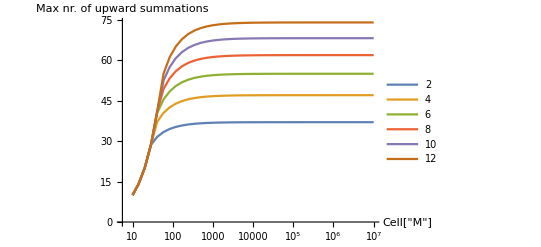

```mathematica
ListLogLinearPlot[TemporalData[XtopdownStart,{M}],PlotRange->Automatic,Joined->True,AxesLabel->{"Cell["M",ExpressionUUID->"05dd0b7c-a6e3-47dc-a719-b50f73b25c4c"]","Max nr. of upward summations"},PlotLegends->pfactor]
```

```mathematica
Ceiling[XtopdownStart[[numM]] ]
```

{38,48,56,62,69,75}

A loose upper bound on the maximal number of iterations in the algorithm follows therefore from going to top-down summation while u=0.5 + ϵ . For that value of u the correct answer is roughly the mean N ·p and thus we must come down again to that value.

```mathematica
Ceiling[XtopdownStart [[numM]] + (XtopdownStart[[numM]]- pfactor)]
```

{73,91,105,116,127,137}

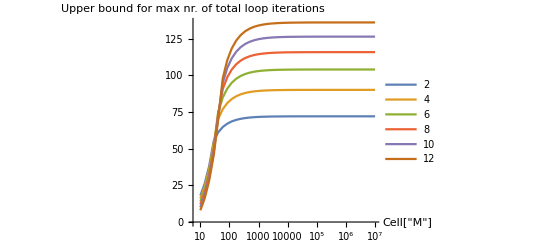

```mathematica
ListLogLinearPlot[TemporalData[Table[2*XtopdownStart[[All,m]]-pfactor[[m]],{m,1,Length[pfactor]}],{M}],PlotRange->Automatic,Joined->True,AxesLabel->{"Cell["M",ExpressionUUID->"1f167b45-d0f0-4b86-900f-9afb37e22c6c"]","Upper bound for max nr. of total loop iterations"},PlotLegends->pfactor]
```

This is, however, a crude upper bound as when u=0.5 + δ_u, where 0<δ_u<0.5, we don’t always sum all the way to the maximal x found earlier. We therefore look at the two extremes, what happens when u=1-2^-53 and what happens when u=0.5 + 2^-53. This gives an idea what happens when between these two extreme values

```mathematica
Xhigh = Table[If[Quiet[(p/m)^(m)]<2^-53,Floor[x/.FindRoot[SetPrecision[BetaRegularized[p/m,x,m-x+1]==2^-53,100],{x,0,m},Method-> "Brent",WorkingPrecision->100][[1]]],m],{m,M},{p,pfactor}];
Xmiddle = Table[If[Quiet[(p/m)^(m)]<2^-53,Floor[x/.FindRoot[SetPrecision[BetaRegularized[p/m,x,m-x+1]==2^-1-2^-53,100],{x,0,m},Method-> "Brent",WorkingPrecision->100][[1]]],m],{m,M},{p,pfactor}];
XtopdownhighStart = XtopdownStart;
XtopdownmiddleStart = Table[If[Quiet[(p/m)^(m)]<10^-17*(2^-1-2^-53),x/.FindRoot[SetPrecision[(1.0-p/m)^(m-x)*(p/m)^(x)*Binomial[m,x]==10^-17*(2^-1-2^-53),100],{x,0,m},Method-> "Brent",WorkingPrecision->100][[1]],m],{m,M},{p,pfactor}];
```

We can see that the most total number of summations is done when u=1-2^-53, but that it is nearly equal to the number of summations when u=0.5+2^-53.

```mathematica
2*Ceiling[XtopdownhighStart[[numM]]] - Xhigh[[numM]]
2*Ceiling[XtopdownmiddleStart[[numM]]]-Xmiddle[[numM]]
```

{54,67,77,83,93,100}

{46,60,70,78,86,94}

If we, however, look at the number of summations just in the top-down phase of the summation we see that this is maximal when u=0.5+2^-53.

```mathematica
Ceiling[XtopdownhighStart[[numM]]] - Xhigh[[numM]]
Ceiling[XtopdownmiddleStart[[numM]]]-Xmiddle[[numM]]
```

{16,19,21,21,24,25}

{22,28,32,35,38,41}

Plot how the max number of loop iterations for fixed M·p changes as M increases.

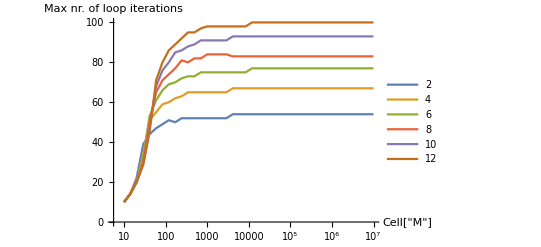

```mathematica
ListLogLinearPlot[TemporalData[2*Ceiling[XtopdownhighStart] - Xhigh,{M}],PlotRange->Automatic,Joined->True,AxesLabel->{"Cell["M",ExpressionUUID->"9fc3ec5f-26cf-4fe4-9d86-44ca540a052f"]","Max nr. of loop iterations"},PlotLegends->pfactor]
```

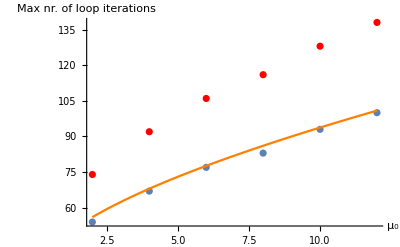

```mathematica
(* Sharp upperbound for max nr of iterations *)
p1 = ListPlot[Transpose[{pfactor,2*Ceiling[XtopdownhighStart[[numM]]] - Xhigh[[numM]]}]];
(* Loose upper bound for max nr *)
p2 = ListPlot[Transpose[{pfactor,2*Ceiling[XtopdownhighStart[[numM]]] -pfactor}],PlotStyle->Red];
(* Crude approximation for the sharper max nr *)
p3 = Plot[30+x +17*Sqrt[x],{x,Min[pfactor],Max[pfactor]},PlotStyle->Orange];
Show[p1,p2,p3,AxesLabel->{"μ_0","Max nr. of loop iterations"},PlotRange->Full]
```

#### Summation terms for small values of M·(1-p)

Define the vector containing the number of trials M and the relation between p and M, i.e. 1-p = α/M where α is an element of pfactor vector

```mathematica
numM = 40;
M = N[Round[logspace[2,7,numM]]];
pfactor = Table[m,{m,2,12,2}];
```

!! First we note that when M·(1-p)<<1 we will generally swap p,q and u,v !!

Now the maximum number of summations follows from the observation that if originally u=2^-1074 we need to do the most summations (when u=0 we simply have x=0) and actually might have to use the top-down summation (if v>0.5). Note that for the top-down summation the limiting number of upward iterations we have to do before we come down again follows from the following:
Now we stop the upward sum when x satisfies δ^*(1-v)=δ^*u=Prob(x,M,p) so we find the maximal x by solving for x the equation 10^-17·2^-1074=Prob(x,M,p) for various M.

```mathematica
XtopdownStart = Table[If[10^17*Quiet[(p/m)^m] <2^-1074, m-x/.FindRoot[SetPrecision[10^17*(p/m)^(m-x)*(1.0-p/m)^(x)*Binomial[m,x]==2^-1074,100],{x,-2,m},Method-> "Brent",WorkingPrecision->100][[1]],
m],{m,M},{p,pfactor}];
```

General::munfl: 0.01111111111111111153515462746099728974513709545135498046875^182. is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.-4.940656458412465441765687928682213723650598026143247644255856825006755072702087518652998363616359924×10^-324 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0082644628099173556012857488894951529800891876220703125^244. is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
Ceiling[XtopdownStart[[numM]]]
```

{213,249,275,296,315,332}

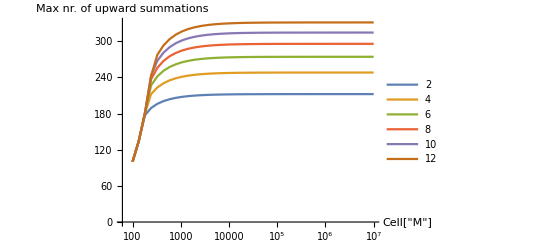

```mathematica
ListLogLinearPlot[TemporalData[XtopdownStart,{M}],PlotRange->Automatic,Joined->True,AxesLabel->{"Cell["M",ExpressionUUID->"86afed41-518b-44e1-8f3c-7422deaafe18"]","Max nr. of upward summations"},PlotLegends->pfactor]
```

Upper bound on the maximal number of iterations in the algorithm are therefore going to top-down summation while v=0.5 + ϵ . For that value of v the correct answer is roughly the mean N ·p and thus we must come down again to that value.

```mathematica
Round[XtopdownStart [[numM]] + (XtopdownStart[[numM]]- pfactor)]
```

{423,492,542,583,619,650}

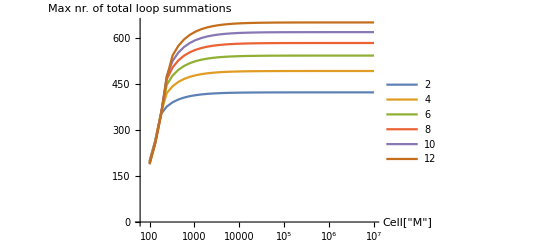

```mathematica
ListLogLinearPlot[TemporalData[Table[2*XtopdownStart[[All,m]]-pfactor[[m]],{m,1,Length[pfactor]}],{M}],PlotRange->Automatic,Joined->True,AxesLabel->{"Cell["M",ExpressionUUID->"d0806fc9-8258-4e8c-b6ad-cb746a1aefc3"]","Max nr. of total loop summations"},PlotLegends->pfactor]
```

This is, however, a crude upper bound as when v=0.5 + δ_u, where 0<δ_u<0.5, we don’t always sum all the way to the maximal x found earlier. We therefore look at the two extremes, what happens when v=1-2^-1074 and what happens when v=0.5 + 2^-53. This gives an idea what happens when between these two extreme values

```mathematica
Xhigh = Table[If[Quiet[(p/m)^(m)]<2^-1074,Floor[x/.FindRoot[SetPrecision[BetaRegularized[p/m,x,m-x+1]==2^-1074,100],{x,0,m},Method-> "Brent",WorkingPrecision->100][[1]]],m],{m,M},{p,pfactor}];
Xmiddle = Table[If[Quiet[(p/m)^(m)]<2^-53,Floor[x/.FindRoot[SetPrecision[BetaRegularized[p/m,x,m-x+1]==2^-1-2^-53,100],{x,0,m},Method-> "Brent",WorkingPrecision->100][[1]]],m],{m,M},{p,pfactor}];
XtopdownhighStart = XtopdownStart;
XtopdownmiddleStart = Table[If[Quiet[(p/m)^(m)]<10^-17*(2^-1-2^-53),m-x/.FindRoot[SetPrecision[(p/m)^(m-x)*(1.0-p/m)^(x)*Binomial[m,x]==10^-17*(2^-1-2^-53),100],{x,-1,m},Method-> "Brent",WorkingPrecision->100][[1]],m],{m,M},{p,pfactor}];
```

General::munfl: 0.01111111111111111153515462746099728974513709545135498046875^181. is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0082644628099173556012857488894951529800891876220703125^243. is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.016528925619834711202571497778990305960178375244140625^243. is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

We can see that the most total number of summations is done when u=1-2^-53, but that it is of the same order of magnitude as when u=0.5+2^-53.

```mathematica
2*Ceiling[XtopdownhighStart[[numM]]] - Xhigh[[numM]]
2*Ceiling[XtopdownmiddleStart[[numM]]]-Xmiddle[[numM]]
```

{223,260,287,308,327,345}

{46,60,70,78,86,94}

If we, however, look at the number of summations just in the top-down phase of the summation we see that this is maximal when u=0.5+2^-53.

```mathematica
Ceiling[XtopdownhighStart[[numM]]] - Xhigh[[numM]]
Ceiling[XtopdownmiddleStart[[numM]]]-Xmiddle[[numM]]
```

{10,11,12,12,12,13}

{22,28,32,35,38,41}

Plot how the max number of loop iterations for fixed M·(1-p) increases.

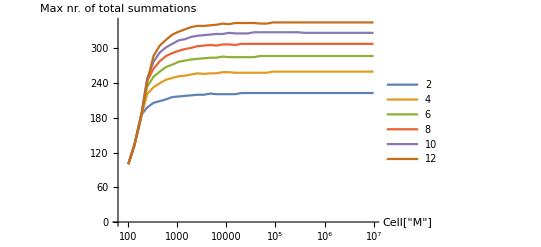

```mathematica
ListLogLinearPlot[TemporalData[2*Ceiling[XtopdownhighStart] - Xhigh,{M}],PlotRange->Automatic,Joined->True,AxesLabel->{"Cell["M",ExpressionUUID->"ae1c8e8e-bbf3-4676-9214-bc021e3bde1d"]","Max nr. of total summations"},PlotLegends->pfactor]
```

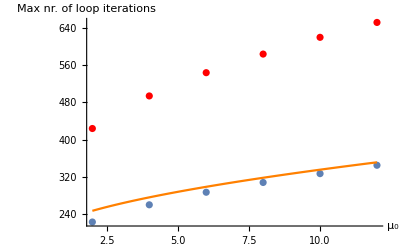

```mathematica
(* Sharp upper bound for max nr of iterations *)
p1 = ListPlot[Transpose[{pfactor,2*Ceiling[XtopdownhighStart[[numM]]] -(1)* Xhigh[[numM]]}]];
(* Loose upper bound for max nr *)
p2 = ListPlot[Transpose[{pfactor,2*Ceiling[XtopdownhighStart[[numM]]] -pfactor}],PlotStyle->Red];
(* Crude approximation for the sharper max nr *)
p3 = Plot[180 + x + 46*Sqrt[x],{x,Min[pfactor],Max[pfactor]},PlotStyle->Orange];
Show[p1,p2,p3,AxesLabel->{"μ_0","Max nr. of loop iterations"},PlotRange->Full]
```

## Limit on summations for given M·p or M·(1-p) in single precision

#### Summation terms for small values of M·p

Define the vector containing the number of trials M and the relation between p and M, i.e. p = α/M where α is an element of pfactor vector

```mathematica
numM = 40;
M = N[Round[logspace[1,7,numM]]];
pfactor = Table[m,{m,2,14,2}];
```

Now the maximum number of upward summations follows from the observation that if u=1-2^-24 we need to do the most summations (when u=1 we simply have x=M) and actually might have to use the top-down summation (if u>0.5). Note that for the top-down summation the limiting number of upward iterations we have to do before we come down again can be derived from the following:
We stop the upward sum when x satisfies δ^*(1-u)=Prob(x,M,p) so we find the maximal x by solving for x the equation 10^-8·2^-53=Prob(x,M,p) for various M.

```mathematica
XtopdownStart = Table[If[Quiet[(p/m)^(m)]<10^-8*2^-24,x/.FindRoot[SetPrecision[(1.0-p/m)^(m-x)*(p/m)^(x)*Binomial[m,x]==10^-8*2^-24,100],{x,0,m},Method-> "Brent",WorkingPrecision->100][[1]],m],{m,M},{p,pfactor}];
```

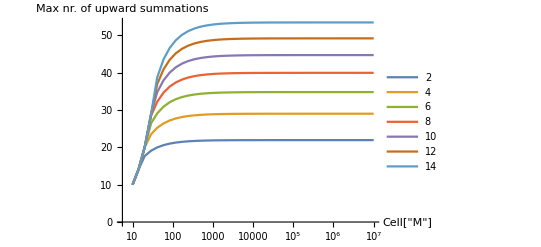

```mathematica
ListLogLinearPlot[TemporalData[XtopdownStart,{M}],PlotRange->Automatic,Joined->True,AxesLabel->{"Cell["M",ExpressionUUID->"cdb50858-4a93-4e58-affe-5660edd94eee"]","Max nr. of upward summations"},PlotLegends->pfactor]
```

```mathematica
Ceiling[XtopdownStart[[numM]] ]
```

{22,30,35,40,45,50,54}

A loose upper bound on the maximal number of iterations in the algorithm follows therefore from going to top-down summation while u=0.5 + ϵ . For that value of u the correct answer is roughly the mean N ·p and thus we must come down again to that value.

```mathematica
Ceiling[XtopdownStart [[numM]] + (XtopdownStart[[numM]]- pfactor)]
```

{42,55,64,72,80,87,93}

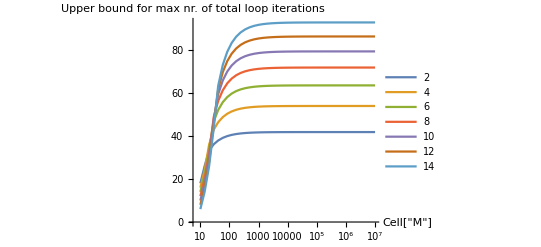

```mathematica
ListLogLinearPlot[TemporalData[Table[2*XtopdownStart[[All,m]]-pfactor[[m]],{m,1,Length[pfactor]}],{M}],PlotRange->Automatic,Joined->True,AxesLabel->{"Cell["M",ExpressionUUID->"42c1574d-6216-4e7d-b47d-95f2696e59ea"]","Upper bound for max nr. of total loop iterations"},PlotLegends->pfactor]
```

This is, however, a crude upper bound as when u=0.5 + δ_u, where 0<δ_u<0.5, we don’t always sum all the way to the maximal x found earlier. We therefore look at the two extremes, what happens when u=1-2^-24 and what happens when u=0.5 + 2^-24. This gives an idea what happens when between these two extreme values

```mathematica
Xhigh = Table[If[Quiet[(p/m)^(m)]<2^-24,Floor[x/.FindRoot[SetPrecision[BetaRegularized[p/m,x,m-x+1]==2^-24,100],{x,0,m},Method-> "Brent",WorkingPrecision->100][[1]]],m],{m,M},{p,pfactor}];
Xmiddle = Table[If[Quiet[(p/m)^(m)]<2^-24,Floor[x/.FindRoot[SetPrecision[BetaRegularized[p/m,x,m-x+1]==2^-1-2^-24,100],{x,0,m},Method-> "Brent",WorkingPrecision->100][[1]]],m],{m,M},{p,pfactor}];
XtopdownhighStart = XtopdownStart;
XtopdownmiddleStart = Table[If[Quiet[(p/m)^(m)]<10^-8*(2^-1-2^-24),x/.FindRoot[SetPrecision[(1.0-p/m)^(m-x)*(p/m)^(x)*Binomial[m,x]==10^-8*(2^-1-2^-24),100],{x,p-1,m+1},Method-> "Brent",WorkingPrecision->100][[1]],m],{m,M},{p,pfactor}];
```

We can see that the most total number of summations is done when u=1-2^-24, but that it is nearly equal to the number of summations when u=0.5+2^-24.

```mathematica
2*Ceiling[XtopdownhighStart[[numM]]] - Xhigh[[numM]]
2*Ceiling[XtopdownmiddleStart[[numM]]]-Xmiddle[[numM]]
```

{31,42,47,53,59,66,70}

{28,38,44,52,58,62,68}

If we, however, look at the number of summations just in the top-down phase of the summation we see that this is maximal when u=0.5+2^-24.

```mathematica
Ceiling[XtopdownhighStart[[numM]]] - Xhigh[[numM]]
Ceiling[XtopdownmiddleStart[[numM]]]-Xmiddle[[numM]]
```

{9,12,12,13,14,16,16}

{13,17,19,22,24,25,27}

Plot how the max number of loop iterations for fixed M·p changes as M increases.

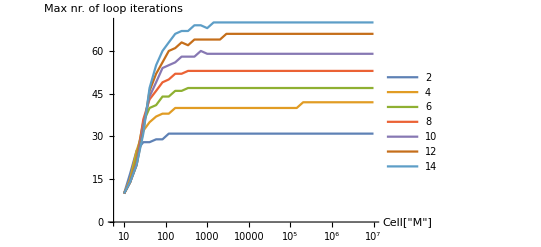

```mathematica
ListLogLinearPlot[TemporalData[2*Ceiling[XtopdownhighStart] - Xhigh,{M}],PlotRange->Automatic,Joined->True,AxesLabel->{"Cell["M",ExpressionUUID->"8dac5236-ff59-4d1d-ade9-3341283dcd44"]","Max nr. of loop iterations"},PlotLegends->pfactor]
```

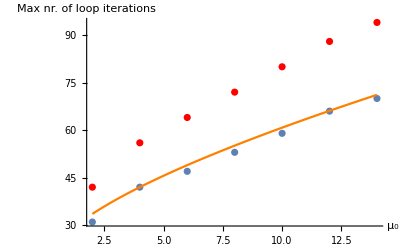

```mathematica
(* Sharp upperbound for max nr of iterations *)
p1 = ListPlot[Transpose[{pfactor,2*Ceiling[XtopdownhighStart[[numM]]] - Xhigh[[numM]]}]];
(* Loose upper bound for max nr *)
p2 = ListPlot[Transpose[{pfactor,2*Ceiling[XtopdownhighStart[[numM]]] -pfactor}],PlotStyle->Red];
(* Crude approximation for the sharper max nr *)
p3 = Plot[16+x +11*Sqrt[x],{x,Min[pfactor],Max[pfactor]},PlotStyle->Orange];
Show[p1,p2,p3,AxesLabel->{"μ_0","Max nr. of loop iterations"},PlotRange->Full]
```

#### Summation terms for small values of M·(1-p)

Define the vector containing the number of trials M and the relation between p and M, i.e. 1-p = α/M where α is an element of pfactor vector

```mathematica
numM = 40;
M = N[Round[logspace[1,7,numM]]];
pfactor = Table[m,{m,2,14,2}];
```

!! First we note that when M·(1-p)<<1 we will generally swap p,q and u,v !!

Now the maximum number of summations follows from the observation that if originally u=2^-149 we need to do the most summations (when u=0 we simply have x=0) and actually might have to use the top-down summation (if v>0.5). Note that for the top-down summation the limiting number of upward iterations we have to do before we come down again follows from the following:
Now we stop the upward sum when x satisfies δ^*(1-v)=δ^*u=Prob(x,M,p) so we find the maximal x by solving for x the equation 10^-8·2^-149=Prob(x,M,p) for various M.

```mathematica
XtopdownStart = Table[If[Quiet[(p/m)^m] <2^-149*10^-8, x/.FindRoot[SetPrecision[(p/m)^(x)*(1.0-p/m)^(m-x)*Binomial[m,x]==2^-149*10^-8,100],{x,0,m},Method-> "Brent",WorkingPrecision->100][[1]],
m],{m,M},{p,pfactor}];
```

```mathematica
Ceiling[XtopdownStart[[numM]]]
```

{52,65,75,83,91,98,104}

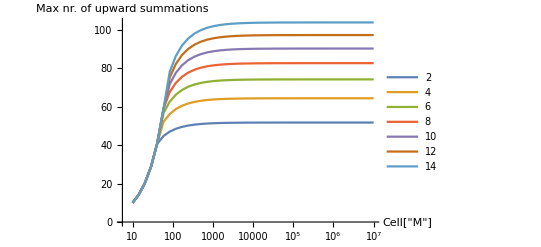

```mathematica
ListLogLinearPlot[TemporalData[XtopdownStart,{M}],PlotRange->Automatic,Joined->True,AxesLabel->{"Cell["M",ExpressionUUID->"9a6ad93d-18c8-4455-a242-52ad34461e16"]","Max nr. of upward summations"},PlotLegends->pfactor]
```

Upper bound on the maximal number of iterations in the algorithm are therefore going to top-down summation while v=0.5 + ϵ . For that value of v the correct answer is roughly the mean N ·p and thus we must come down again to that value.

```mathematica
Round[XtopdownStart [[numM]] + (XtopdownStart[[numM]]- pfactor)]
```

{102,125,143,157,171,183,194}

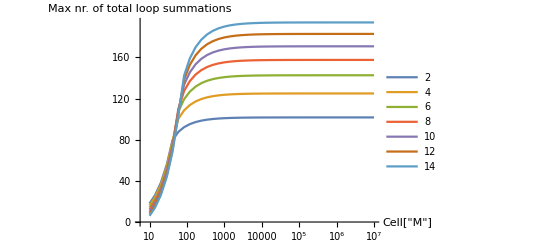

```mathematica
ListLogLinearPlot[TemporalData[Table[2*XtopdownStart[[All,m]]-pfactor[[m]],{m,1,Length[pfactor]}],{M}],PlotRange->Automatic,Joined->True,AxesLabel->{"Cell["M",ExpressionUUID->"fe5839a4-8a7f-421a-bac2-aa6fa10df00d"]","Max nr. of total loop summations"},PlotLegends->pfactor]
```

This is, however, a crude upper bound as when v=0.5 + δ_u, where 0<δ_u<0.5, we don’t always sum all the way to the maximal x found earlier. We therefore look at the two extremes, what happens when v=1-2^-149 and what happens when v=0.5 + 2^-24. This gives an idea what happens when between these two extreme values

```mathematica
Xhigh = Table[If[Quiet[(p/m)^(m)]<2^-149,Floor[x/.FindRoot[SetPrecision[BetaRegularized[p/m,x,m-x+1]==2^-149,100],{x,0,m},Method-> "Brent",WorkingPrecision->100][[1]]],m],{m,M},{p,pfactor}];
Xmiddle = Table[If[Quiet[(p/m)^(m)]<2^-24,Floor[x/.FindRoot[SetPrecision[BetaRegularized[p/m,x,m-x+1]==2^-1-2^-24,100],{x,0,m},Method-> "Brent",WorkingPrecision->100][[1]]],m],{m,M},{p,pfactor}];
XtopdownhighStart = XtopdownStart;
XtopdownmiddleStart = Table[If[Quiet[(p/m)^(m)]<10^-8*(2^-1-2^-24),x/.FindRoot[SetPrecision[(p/m)^(x)*(1.0-p/m)^(m-x)*Binomial[m,x]==10^-8*(2^-1-2^-24),100],{x,p-1,m},Method-> "Brent",WorkingPrecision->100][[1]],m],{m,M},{p,pfactor}];
```

We can see that the most total number of summations is done when u=1-2^-24, but that it is of the same order of magnitude to the number of summations when u=0.5+2^-24.

```mathematica
2*Ceiling[XtopdownhighStart[[numM]]] - Xhigh[[numM]]
2*Ceiling[XtopdownmiddleStart[[numM]]]-Xmiddle[[numM]]
```

{58,73,84,92,101,108,114}

{28,38,44,52,58,62,68}

If we, however, look at the number of summations just in the top-down phase of the summation we see that this is maximal when u=0.5+2^-24.

```mathematica
Ceiling[XtopdownhighStart[[numM]]] - Xhigh[[numM]]
Ceiling[XtopdownmiddleStart[[numM]]]-Xmiddle[[numM]]
```

{6,8,9,9,10,10,10}

{13,17,19,22,24,25,27}

Plot how the max number of loop iterations for fixed M·(1-p) increases.

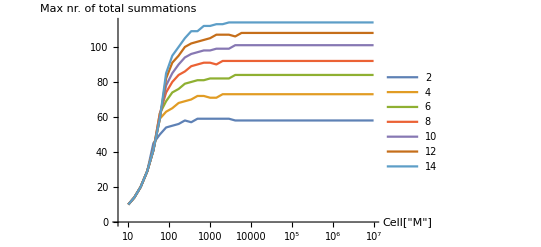

```mathematica
ListLogLinearPlot[TemporalData[2*Ceiling[XtopdownhighStart] - Xhigh,{M}],PlotRange->Automatic,Joined->True,AxesLabel->{"Cell["M",ExpressionUUID->"388d5bb0-a62c-4816-bf6b-1fc07f423825"]","Max nr. of total summations"},PlotLegends->pfactor]
```

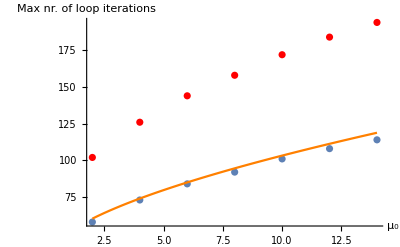

```mathematica
(* Sharp upper bound for max nr of iterations *)
p1 = ListPlot[Transpose[{pfactor,2*Ceiling[XtopdownhighStart[[numM]]] -(1)* Xhigh[[numM]]}]];
(* Loose upper bound for max nr *)
p2 = ListPlot[Transpose[{pfactor,2*Ceiling[XtopdownhighStart[[numM]]] -pfactor}],PlotStyle->Red];
(* Crude approximation for the sharper max nr *)
p3 = Plot[30 + x + 20*Sqrt[x],{x,Min[pfactor],Max[pfactor]},PlotStyle->Orange];
Show[p1,p2,p3,AxesLabel->{"μ_0","Max nr. of loop iterations"},PlotRange->Full]
```